```mathematica
potential[r_]:=-1/r
```

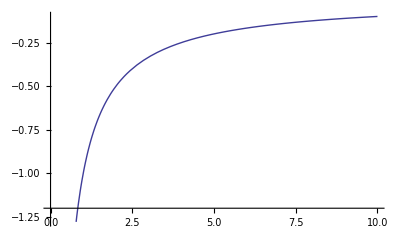

```mathematica
Plot[potential[r],{r,0,10}]
```

```mathematica
gaussian[r_]:=Exp[-a*r*r]
```

```mathematica
Integrate[gaussian[r]*gaussian[r]*r*r,{r,0,Infinity}]
```

If[Re[a]>0,(√(π/2))/(8 a^(3/2)),Integrate[ⅇ^(-2 a r^2) r^2,{r,0,∞},Assumptions→Re[a]≤0]]

```mathematica
ngaussian[r_,a_]:=(√(π/2))/(8 a^(3/2))*Exp[-a*r*r]
```

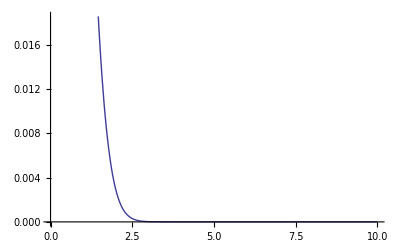

```mathematica
Plot[ngaussian[r,1],{r,0,10}]
```

```mathematica
ngaussian[0.5,1.1]
```

0.103145